## Gaussian moving potential

#### Gaus

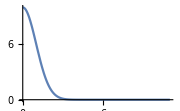

```mathematica
Off[General::munfl]
MovingGaus[a_, b_, c_, x_, ω_, t_, ϕ_]:= Chop[a*Chop[Exp[-(x- b*Sin[ω*t+ϕ])^2/(2*c^2)]]];
Plot[MovingGaus[10, 5, 1, x, 1, 0, 0], {x, 0, 11}, PlotRange->All, ImageSize-> Small]
```

#### Calculate and subtract time average

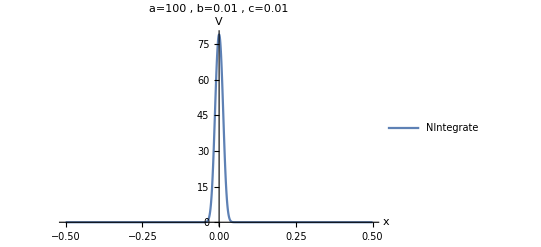

```mathematica
TimeAverage[a_, b_, c_, x_]:= a/(2π)*Chop[Exp[(-2*x^2 - b^2)/(4*c^2)]]*Chop[NIntegrate[Chop[Exp[(x*b*Sin[t])/c^2]]*Chop[Exp[(b^2*Cos[2*t])/(4 c^2)]], {t, 0, 2π}]];a = 100; b = 0.01; c = 0.01;Plot[{TimeAverage[a, b, c, x]} , {x, -0.5, 0.5}, PlotRange->All, PlotLegends->{"NIntegrate"}, AxesLabel->{x, V}, PlotLabel->("a="<>ToString[a]
", b="<>ToString[b]", c="<>ToString[c])]
```

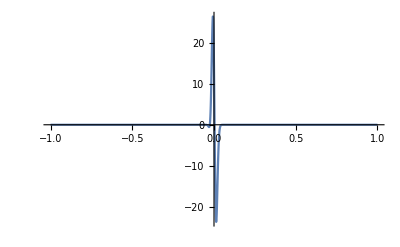

```mathematica
MovingGausSubtractTimeAverage[a_, b_, c_, x_, ω_, t_, ϕ_]:= MovingGaus[a, b, c,x, ω, t, ϕ] - TimeAverage[a, b, c, x];
Plot[MovingGausSubtractTimeAverage[a, b, c, x, 3, 3*Pi/8, 0], {x, -1, 1}, PlotRange->All]
```

```mathematica
HtMovingGausSubtractTimeAverage[Nl_,centrex_, a_, b_, c_,  ω_, t_, ϕ_]:=Table[If[i==j, MovingGausSubtractTimeAverage[a, b, c, i -centrex,  ω, t, ϕ],If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
HtMovingGausSubtractTimeAverage[12,6, 10, 0.5, 0.3, 1, 0, 0]//MatrixForm
```

(0. | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0. | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0. | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | -5.15379×10^-6 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | -0.528501 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 4.38606 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | -0.528501 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | -5.15379×10^-6 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0. | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0. | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0. | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0.)

#### Oscillate one energy offset term only

```mathematica
HtOneSiteCosineModulated[Nl_, centresite_, a_, ω_, t_, ϕ_]:=Table[If[i== centresite && i ==j, a*Cos[ω*t + ϕ],If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
HtOneSiteCosineModulated[7,4, a, ω, t, ϕ]//MatrixForm
```

(0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | -1 | a Cos[ϕ+t ω] | -1 | 0 | 0
0 | 0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | -1 | 0)

#### Time independent Hamiltonian with altered hoping

```mathematica
SL[Nl_, centre_, hoppings_, A_]:= 
Module[{radius, A2},
radius = Length[A];
A2 = Join[A , Reverse[A]];
Table[If[MemberQ[Range[centre-radius, centre+radius-1], i], A2[[i-(centre-radius - 1)]], hoppings], {i, 1, Nl-1}]];
HTimeIndependent[Nl_, centre_, hoppings_,  A_]:= Table[If[Abs[i-j]==1,SL[Nl, centre, hoppings, A][[Min[i, j]]],0], {i,1,Nl},{j,1,Nl}];
HTimeIndependent[12, 6, -1, {-0.7, -0.1, -0.01}] // MatrixForm
```

(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | -0.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.7 | 0 | -0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.1 | 0 | -0.01 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.01 | 0 | -0.01 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.01 | 0 | -0.1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.1 | 0 | -0.7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.7 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

#### Solve Schrodinger Eq’s

```mathematica
ClearAll@ψ1;
ClearAll@ψ2;
(*conditions*)
tf = 30; Nl = 51; 
atomsitestart = 25;

(*time dependent potential parameters*)
a = 25;  ω=1.5; ϕ = 0;
T = 2π/ω;
centreM = 25;

(*extra parameters for moving gaussian*)
b = 0.1; c = 0.1;

(*stationary hopping parameters*)
centreS = 25;
hoppings = -1;
A = {-1};

ψ0 = Table[If[i==atomsitestart,1,0],{i,1,Nl}];
s1=NDSolve[{I D[ψ1[t], t]== HtMovingGausSubtractTimeAverage[Nl, centreM, a,  b, c, ω, t, ϕ].ψ1[t], ψ1[0] == ψ0}, ψ1, {t, 0, tf}];
ψ1[t_]=Evaluate[ψ1[t]/.s1]; 
s2=NDSolve[{I D[ψ2[t], t]== HTimeIndependent[Nl, centreS, hoppings, A].ψ2[t], ψ2[0] == ψ0}, ψ2, {t, 0, tf}];
ψ2[t_]=Evaluate[ψ2[t]/.s2];
```

```mathematica
(*Table[Plot[Norm[ ψ[t][[1, i]]], {t, 0, 8*Pi / ω}, PlotRange->Full, PlotLabel -> i - midx, AxesLabel->{"t", ""}], {i, midx , midx+5}]*)
(*Table[Plot[Norm[ ψ[t][[1, i]]], {t, 0, tf}, PlotRange->{{0, 30}, {0, 1}}, PlotLabel -> i - midx, AxesLabel->{"t", ""}], {i, midx , midx+5}]*)
```

#### Plot things

```mathematica
siteside = Floor[Nl/2];
siteside = 40; tmax = 20;

xrow=Table[If[Divisible[i, Round[10*T]]==True,i/Round[10*T],""],{i,0,tf*10}];
ycolumn=Table[ If[Divisible[i, 10]==True,i,""],{i,0,siteside*2}];
xticksMatrix=MapIndexed[{#2[[1]],#}&,xrow];
yticksMatrix=MapIndexed[{#2[[1]],#}&,ycolumn];
xticksPlot = Table[i,{i,0,tf,T}];

dx = 0.1;
difference = Total[Table[Norm[ψ1[t][[1, i]]] - Norm[ψ2[t][[1, i]]], {i, 1, Nl}, {t, 0, tmax, dx}]];
Print["Period: ", N[2*Pi/ω]]
Print["Total difference: ",  Total[Abs /@ difference] *dx]
Print["Max difference: ",  Max[Abs /@ difference]]

(* Plot difference *)
(*MatrixPlot[Table[Norm[ψ1[t][[1, i]] - ψ2[t][[1, i]]], {i, 1, Nl}, {t, 0, tmax, 0.1}],FrameLabel->{"site","t   (T)"},ColorFunction->"NeonColors", ColorFunctionScaling->False,  ImageSize->Large, FrameTicks->{{yticksMatrix,yticksMatrix},{xticksMatrix,xticksMatrix}}]
ListLinePlot[Transpose[{Range[0, tmax, dx],difference}], PlotStyle->Thick, ColorFunction->Function[{x, y}, ColorData["NeonColors"][y]], ColorFunctionScaling->False, Ticks->{xticksPlot, Automatic}, GridLines->{xticksPlot, None}]*)

(*cant remember what this plotted*)
(*Plot[Total[Table[Norm[ψ1[t][[1, i]]] - Norm[ψ2[t][[1, i]]], {i, 1, Nl}]], {t, 0, tmax}, PlotStyle->Thick, ColorFunction->Function[{x, y}, ColorData["NeonColors"][y]], ColorFunctionScaling->False, Ticks->{xticksPlot, Automatic}, GridLines->{xticksPlot, None}]*)

Print["Localisation: ",Total[Table[Norm[ψ1[t][[1, atomsitestart]]], {t, 0, tmax, 0.1}]]/(tmax*10+1)]

 MatrixPlot[Table[Norm[ψ1[t][[1, i]]], {i, 1, Nl}, {t, 0, tmax, 0.1}], FrameLabel->{"site","oscillations"}, FrameTicks->{{yticksMatrix,yticksMatrix},{xticksMatrix,xticksMatrix}}, ImageSize-> Large, ColorFunctionScaling->False, PlotLabel->"Time Dependent"]
(*MatrixPlot[Table[Norm[ψ2[t][[1, i]]], {i, 1, Nl}, {t, 0, tmax, 0.1}], FrameLabel->{"site","t   (T)"}, FrameTicks->{{yticksMatrix,yticksMatrix},{xticksMatrix,xticksMatrix}}, ImageSize-> Large, ColorFunctionScaling->False, PlotLabel->"Time Independent"]*)
```

Period: 4.18879

Total difference: 3.71566

Max difference: 0.511216

Localisation: 0.330924

-Graphics-

#### Calculate degree of localisation

```mathematica
Total[Table[Norm[ψ1[t][[1, 40]]], {t, 0, tmax, 0.1}]]/(tmax*10+1)
```

0.0259622

#### Calculate U(T)

```mathematica
ψ0 = Table[If[i==1,1,0],{i,1,Nl}];
ψ0
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}